# 均匀带电圆盘的数值解

## 概述

通过数值求解的方法获得了均匀带电圆盘的电势分布以及电场分布图。主要的参考资料是	广东第二师范学院 沈华嘉 发表的《均匀带电圆盘电场的数值研究》。
链接如下：

```mathematica
Hyperlink["均匀带电圆盘电场的数值研究","http://www.doc88.com/p-7704590523352.html"]
```

[均匀带电圆盘电场的数值研究](http://www.doc88.com/p-7704590523352.html)

## 公式准备

所要研究的电场的可以用如下公式描述：
-Graphics-

编程实现如下：

```mathematica
f[x_,z_,ρ_]:=NIntegrate[ρ/(ρ^2+x^2+z^2-2x*ρ*Cos[φ])^(1/2),{φ,0,2Pi}]
```

```mathematica
U[{x_,z_}]:=NIntegrate[f[x,z,ρ],{ρ,0,1}]
```

这里我们试图求出它的解析表达式：

```mathematica
f[x,z,ρ]
```

ConditionalExpression[(2 EllipticK[-(4 x ρ)/(z^2+(x-ρ)^2)])/(√(z^2+(x-ρ)^2))+(2 EllipticK[(4 x ρ)/(z^2+(x+ρ)^2)])/(√(z^2+(x+ρ)^2)),(Re[(x^2+z^2+ρ^2)/(x ρ)]≥2||Re[(x^2+z^2+ρ^2)/(x ρ)]≤-2||(x^2+z^2+ρ^2)/(x ρ)∉ℝ)&&Re[z^2+(x-ρ)^2]>0&&Re[z^2+(x+ρ)^2]>0]

可以看到解析表达式极为繁杂，故而采用数值求解法。

```mathematica
Integrate[(2 EllipticK[-(4 x ρ)/(z^2+(x-ρ)^2)])/(√(z^2+(x-ρ)^2))+(2 EllipticK[(4 x ρ)/(z^2+(x+ρ)^2)])/(√(z^2+(x+ρ)^2)),{ρ,0,1}]
```

∫_0^1 ((2 EllipticK[-(4 x ρ)/(z^2+(x-ρ)^2)])/(√(z^2+(x-ρ)^2))+(2 EllipticK[(4 x ρ)/(z^2+(x+ρ)^2)])/(√(z^2+(x+ρ)^2)))ⅆρ

```mathematica
Plot3D[∫_0^1 ((2 EllipticK[-(4 x ρ)/(z^2+(x-ρ)^2)])/(√(z^2+(x-ρ)^2))+(2 EllipticK[(4 x ρ)/(z^2+(x+ρ)^2)])/(√(z^2+(x+ρ)^2)))ⅆρ,{x,-2,2},{z,-2,2}]
```

## 数值求解编程

在指定范围内定义数组，作为离散化的网格格点：

```mathematica
a=Table[{x,y},{x,-2,2,0.1},{y,-2,2,0.1}];
```

对每个格点进行数值积分，这里格点总数1600个，共计用时648秒用DumpSave来存储变量，免得下一次又要重新计算。

```mathematica
k=Map[U[#]&,a,{-2}]//Timing;
```

```mathematica
SetDirectory[$TemporaryDirectory]
```

C:\Users\QQ\AppData\Local\Temp

```mathematica
DumpSave["代做.mx",k];
```

```mathematica
ResetDirectory[];
```

这里定义一个修正函数，用于将格点坐标化为实际坐标。

```mathematica
Redo[x_,y_]:=MapThread[Flatten[{#1,#2}]&,{Level[x,{2}],Level[y,{2}]}];
```

得到格点值以后绘制图形，则为电势的分布图：

```mathematica
ListPlot3D[MapThread[Flatten[{#1,#2}]&,{Level[a,{2}],Level[k[[2]],{2}]}],AxesLabel->{"x","z","U"}]
```

-Graphics3D-

注意！由于格点坐标还没有乘以空间步长，因此x,z两个轴上面的刻度要乘以步长0.1才是真实值！

可以发现做出来的图跟文献上面的图一致，效果非常好！！！
-Graphics-

接下来用Mathematica的差分格式来计算x,z方向的电场分布：

```mathematica
i=Redo[a[[1;;40,1;;40]],10*Differences[k[[2]],{1,0}][[1;;40,1;;40]]];
```

```mathematica
ListPlot3D[i,AxesLabel->{"x","z","E_z"},PlotRange->All]
```

-Graphics3D-

```mathematica
j=Redo[a[[1;;40,1;;40]],10*Differences[k[[2]],{0,1}][[1;;40,1;;40]]];
```

```mathematica
ListPlot3D[j,AxesLabel->{"x","z","E_x"}]
```

-Graphics3D-

随后将两个方向的电场平方相加，并且绘制图形：

```mathematica
m=100*(Differences[k[[2]],{0,1}]^2)[[1;;40,1;;40]];
```

```mathematica
n=100*(Differences[k[[2]],{1,0}]^2)[[1;;40,1;;40]];
```

```mathematica
l=Redo[a[[1;;40,1;;40]],Sqrt[m+n]];
```

```mathematica
ListPlot3D[l,AxesLabel->{"x","z","E"},PlotRange->All]
```

-Graphics3D-

跟文献结果一致。

```mathematica
p=(Differences[k[[2]],{1,0}])[[1;;40,1;;40]];
```

```mathematica
q=(Differences[k[[2]],{0,1}])[[1;;40,1;;40]];
```

```mathematica
c=MapThread[{#1,#2}&,{-p,-q},2];
```

利用数据流线图可以作出电场的矢量场图：

```mathematica
Dimensions[c]
```

{40,40,2}

```mathematica
r=MapThread[{#1,#2}&,{Level[a[[1;;40,1;;40]],{2}],Level[c,{2}]}]
```

{{{-2.,-2.},{-0.0259381,-0.0287128}},{{-2.,-1.9},{-0.0280584,-0.029579}},1597,{{1.9,1.9},{0.0280584,0.0308331}}}
 |  |  |  |

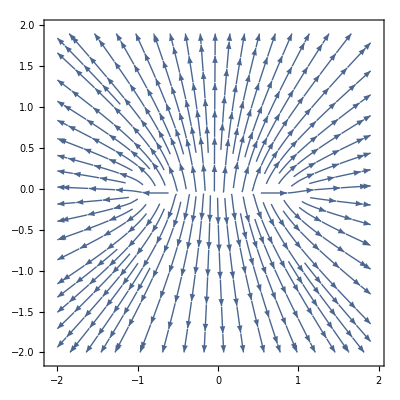

```mathematica
ListStreamPlot[r]
```